## numerical culculations

### test for iteration

```mathematica
FindRoot[(0.23 10^-6)^2==(2 epsilonsi kB T/e^2) Log[1.21 10^15 nn/(1.5 10^15)^2] 1.21 10^15/nn (1/(1.21 10^15+nn)),{nn,10^18}]
```

{nn→2.34601×10^18}

```mathematica
Solve[(0.23 10^-6)^2==2 epsilonsi/e 0.8002941330818842 (1.21 10^15/nn) (1/(1.21 10^15+nn)),nn]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{nn→-4.88673×10^18},{nn→4.88552×10^18}}

```mathematica
kB T/e Log[1.21 10^15 nn/10^15^2]/.nn->7.5666 10^18
```

-11.3719

```mathematica
0.0259 Log[7.6 10^18 1.21 10^15/(1.5 10^10)^2]
```

0.811743

```mathematica
Solve[x^2+x A-B==0,x]
```

{{x→1/2 (-A-√(A^2+4 B))},{x→1/2 (-A+√(A^2+4 B))}}

#### test

```mathematica
nn={10^15};vb={};
For[i=1,i<10,i++,
v=kB T/e Log[1.21 10^15 nn[[i]]/(1.5 10^10)^2];AppendTo[vb,v];
n=(-1.21 10^15 e (0.23 10^-6)^2+√(1.21 10^15) √e (0.23 10^-6) √(8 epsilonsi v+1.21 10^15 e (0.23 10^-6)^2))/(2 e (0.23 10^-6)^2);AppendTo[nn,n];Print[nn,vb];];
nn[[9]]
vb[[9]]
```

{1000000000000000,4.15626×10^18}{0.579231}

{1000000000000000,4.15626×10^18,4.86823×10^18}{0.579231,0.794641}

{1000000000000000,4.15626×10^18,4.86823×10^18,4.88073×10^18}{0.579231,0.794641,0.798729}

{1000000000000000,4.15626×10^18,4.86823×10^18,4.88073×10^18,4.88094×10^18}{0.579231,0.794641,0.798729,0.798795}

{1000000000000000,4.15626×10^18,4.86823×10^18,4.88073×10^18,4.88094×10^18,4.88094×10^18}{0.579231,0.794641,0.798729,0.798795,0.798796}

{1000000000000000,4.15626×10^18,4.86823×10^18,4.88073×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18}{0.579231,0.794641,0.798729,0.798795,0.798796,0.798796}

{1000000000000000,4.15626×10^18,4.86823×10^18,4.88073×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18}{0.579231,0.794641,0.798729,0.798795,0.798796,0.798796,0.798796}

{1000000000000000,4.15626×10^18,4.86823×10^18,4.88073×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18}{0.579231,0.794641,0.798729,0.798795,0.798796,0.798796,0.798796,0.798796}

{1000000000000000,4.15626×10^18,4.86823×10^18,4.88073×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18,4.88094×10^18}{0.579231,0.794641,0.798729,0.798795,0.798796,0.798796,0.798796,0.798796,0.798796}

4.88094×10^18

0.798796

```mathematica
Solve[xn^2==2 esi vbb/q (np/nnn) 1/(np+nnn),nnn][[2,1,2]]
```

(-np q xn^2+√np √q xn √(8 esi vbb+np q xn^2))/(2 q xn^2)

```mathematica
nn={10^20};vb={0.};opt={np->1.21 10^15,xn->0.23 10^-6,q->e,esi->epsilonsi,ni->1.5 10^10};
For[i=1,i<10,i++,v=kB T/e Log[np nn[[i]]/ni^2]/.opt;AppendTo[vb,v];n=(-np q xn^2+√np √q xn √(8 esi v+np q xn^2))/(2 q xn^2)/.opt;AppendTo[nn,n];Print[{nn[[i]],vb[[i]]}];];
```

{100000000000000000000,0.}

{5.11393×10^18,0.876865}

{4.88462×10^18,0.800002}

{4.881×10^18,0.798816}

{4.88094×10^18,0.798796}

{4.88094×10^18,0.798796}

{4.88094×10^18,0.798796}

«2 more identical outputs»

```mathematica
x1=0;x2=0;x3=0;xx={{x1,x2,x3}}//N;err=0.01;
For[i=1,i<20,i++,x1=(14-3 x2+3 x3)/8;x2=(5+2 x1-5 x3)/(-8);x3=(-8-3 x1-5 x2)/(-5);xx1={x1,x2,x3}//N;AppendTo[xx,xx1];Print[xx[[i]]]]
```

{0.,0.,0.}

{1.75,-1.0625,1.5875}

{2.74375,-0.31875,2.9275}

{2.96734,0.462852,3.84326}

{3.01765,1.02262,4.43321}

{3.02897,1.38852,4.8059}

{3.03152,1.62081,5.03972}

{3.03209,1.7668,5.18606}

{3.03222,1.85823,5.27756}

{3.03225,1.91541,5.33476}

{3.03226,1.95116,5.37052}

{3.03226,1.97351,5.39286}

{3.03226,1.98748,5.40683}

{3.03226,1.9962,5.41556}

{3.03226,2.00166,5.42101}

{3.03226,2.00507,5.42442}

{3.03226,2.0072,5.42656}

{3.03226,2.00853,5.42789}

{3.03226,2.00937,5.42872}

QR

```mathematica
Clear["Global`*"];
S[m_]:=Module[{turn=8,ss={},i,q,r},
For[i=1,i<turn,i++,{q,r}=QRDecomposition[m//N];
(*Print[q];Print[r];*)m=r.q;
(*Print[m0];*)AppendTo[ss,m];];Print[ss]]
```

```mathematica
m={{0.,2.},{2.,3.}};S[m]
```

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 2..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

{{{0.,2.},{2.,3.}},{{0.,2.},{2.,3.}},{{0.,2.},{2.,3.}},{{0.,2.},{2.,3.}},{{0.,2.},{2.,3.}},{{0.,2.},{2.,3.}},{{0.,2.},{2.,3.}}}

```mathematica
Clear["Global`*"];turn=10;ss={};m={{2.,2.,4.},{1.,3.,5.},{2.,3.,4.}};For[i=1,i<turn,i++,{q,r}=QRDecomposition[m//N];
(*Print[q];Print[r];*)m=r.q;
(*Print[m0];*)AppendTo[ss,m];];Print[ss];
```

{{{3.75379,7.35491,-2.93124},{0.559387,2.52107,-1.81992},{0.62069,0.413793,-0.827586}},{{2.70812,8.71044,-0.40136},{-0.293681,1.9056,0.0587187},{0.202715,-0.457906,-0.813293}},{{3.7609,7.6477,-2.35665},{0.394386,2.70207,-1.35412},{0.0220002,-0.262605,-0.674352}},{{2.90049,8.53314,1.20782},{-0.21737,2.0361,0.658947},{0.0186554,-0.13228,-0.817801}},{{3.52854,8.01469,-1.70919},{0.201537,2.60453,-0.986826},{0.000915118,-0.0538197,-0.769377}},{{3.06092,8.38155,1.55058},{-0.123716,2.16236,0.811171},{0.00138249,-0.0206107,-0.791548}},{{3.39572,8.14171,-1.59549},{0.100987,2.48845,-0.905116},{0.0000449945,-0.00764381,-0.78365}},{{3.15141,8.31499,1.59338},{-0.0668444,2.24729,0.846819},{0.000091146,-0.00271436,-0.786579}},{{3.3267,8.19484,-1.58503},{0.0513876,2.42149,-0.884329},{2.40581×10^-6,-0.000957719,-0.785551}}}

```mathematica
Clear["Global`*"];
(*ss={};*)turn=10;
S[m_]:=With[{j=turn},ss={};m0=m;For[i=1,i<j,i++,{q,r}=QRDecomposition[m0];m0=r.Transpose[q];AppendTo[ss,m0];];Print[ss[[turn-1]]];]
```

```mathematica
m={{2.,2.,4.},{1.,3.,5.},{2.,3.,4.}};
S[m]
m1={{0.,2.},{2.,3.}};
S[m1]
```

{{8.80916,0.692058,-2.88515},{3.2844×10^-8,0.91668,-0.476822},{1.8589×10^-9,-0.0330147,-0.725844}}

{{4.,0.000038147},{0.000038147,-1.}}

### interpolation

```mathematica
order1y[x_,i_]:=yy[[i]]+(yy[[i+1]]-yy[[i]]) (x-xx[[i]])/(xx[[i+1]]-xx[[i]])
order2y[x_,i_]:=yy[[i]]+(yy[[i+1]]-yy[[i]]) ((x-xx[[i]]) ())/(xx[[i+1]]-xx[[i]])
```

```mathematica
xx={0,1,2};yy={1,3,2};
y[1.5,2]
```

```mathematica
L1=((x-xx[[2]]) (x-xx[[3]]))/((xx[[1]]-xx[[2]]) (xx[[1]]-xx[[3]]));
L2=((x-xx[[1]]) (x-xx[[3]]))/((xx[[2]]-xx[[1]]) (xx[[2]]-xx[[3]]));
L3=((x-xx[[1]]) (x-xx[[2]]))/((xx[[3]]-xx[[1]]) (xx[[3]]-xx[[2]]));
```

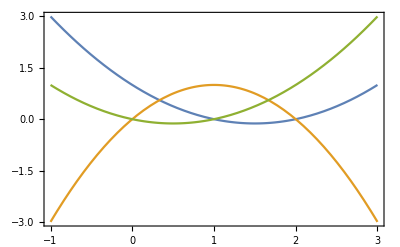

```mathematica
Plot[{L1,L2,L3},{x,-1,3},Frame->True,PlotRange->{{-1,3},{-3,3}}]
```

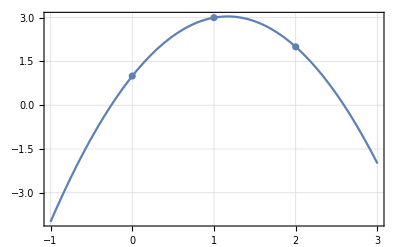

```mathematica
Show[Plot[L1+3 L2+2 L3,{x,-1,3}],ListPlot[{{0,1},{1,3},{2,2}}],Frame->True,GridLines->Automatic]
```

```mathematica
Solve[{1==a L1+b L2+c L3/.x->0,3==a L1+b L2+c L3/.x->1,2==a L1+b L2+c L3/.x->2},{a,b,c}]
```

{{a→1,b→3,c→2}}

```mathematica
f[x_,n_]:=Sum[Subscript[a, i] Product[x-Subscript[b, j],{j,0,i-1}],{i,0,n}]
```

```mathematica
f[x,4]
```

a_0+a_1 (x-b_0)+a_2 (x-b_0) (x-b_1)+a_3 (x-b_0) (x-b_1) (x-b_2)+a_4 (x-b_0) (x-b_1) (x-b_2) (x-b_3)

```mathematica
Solve[{Subscript[y, 0]==f[Subscript[x, 0],3],y2==f[Subscript[x, 1],3]},{Subscript[a, 0],Subscript[a, 1]}]
```

```mathematica
eq1=Subscript[y, 0]==f[x,3]/.x->Subscript[b, 0];
eq2=Subscript[y, 1]==f[x,3]/.x->Subscript[b, 1];
eq3=Subscript[y, 2]==f[x,3]/.x->Subscript[b, 2];
eq4=Subscript[y, 3]==f[x,3]/.x->Subscript[b, 3];
Solve[{eq1,eq2,eq3,eq4},{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}]//Simplify
```

{{a_0→y_0,a_1→(y_0-y_1)/(b_0-b_1),a_2→(b_2 (-y_0+y_1)+b_1 (y_0-y_2)+b_0 (-y_1+y_2))/((b_0-b_1) (b_0-b_2) (b_1-b_2)),a_3→(b_0 (b_0-b_3) b_3 (y_1-y_2)+b_2^2 (b_3 (y_0-y_1)+b_0 (y_1-y_3))+b_1 (b_3^2 (y_0-y_2)+b_0^2 (y_2-y_3)+b_2^2 (-y_0+y_3))+b_2 (b_3^2 (-y_0+y_1)+b_0^2 (-y_1+y_3))+b_1^2 (b_3 (-y_0+y_2)+b_2 (y_0-y_3)+b_0 (-y_2+y_3)))/((b_0-b_1) (b_0-b_2) (b_1-b_2) (b_0-b_3) (b_1-b_3) (b_2-b_3))}}

```mathematica
xxx={-5,-1,0,2};yyy={-2,6,1,3};
a0=yyy[[1]]
a1=(yyy[[1]]-yyy[[2]])/(xxx[[1]]-xxx[[2]])
a2=(xxx[[3]] (-yyy[[1]]+yyy[[2]])+xxx[[2]] (yyy[[1]]-yyy[[3]])+xxx[[1]] (-yyy[[2]]+yyy[[1]]3))/((xxx[[1]]-xxx[[2]]) (xxx[[1]]-xxx[[3]]) (xxx[[2]]-xxx[[3]]))
```

```mathematica
{Subscript[y, 0],(Subscript[y, 0]-Subscript[y, 1])/(Subscript[b, 0]-Subscript[b, 1]),(Subscript[b, 2] (-Subscript[y, 0]+Subscript[y, 1])+Subscript[b, 1] (Subscript[y, 0]-Subscript[y, 2])+Subscript[b, 0] (-Subscript[y, 1]+Subscript[y, 2]))/((Subscript[b, 0]-Subscript[b, 1]) (Subscript[b, 0]-Subscript[b, 2]) (Subscript[b, 1]-Subscript[b, 2])),(Subscript[b, 0] (Subscript[b, 0]-Subscript[b, 3]) Subscript[b, 3] (Subscript[y, 1]-Subscript[y, 2])+Subscript[b, 2]^2 (Subscript[b, 3] (Subscript[y, 0]-Subscript[y, 1])+Subscript[b, 0] (Subscript[y, 1]-Subscript[y, 3]))+Subscript[b, 1] (Subscript[b, 3]^2 (Subscript[y, 0]-Subscript[y, 2])+Subscript[b, 0]^2 (Subscript[y, 2]-Subscript[y, 3])+Subscript[b, 2]^2 (-Subscript[y, 0]+Subscript[y, 3]))+Subscript[b, 2] (Subscript[b, 3]^2 (-Subscript[y, 0]+Subscript[y, 1])+Subscript[b, 0]^2 (-Subscript[y, 1]+Subscript[y, 3]))+Subscript[b, 1]^2 (Subscript[b, 3] (-Subscript[y, 0]+Subscript[y, 2])+Subscript[b, 2] (Subscript[y, 0]-Subscript[y, 3])+Subscript[b, 0] (-Subscript[y, 2]+Subscript[y, 3])))/((Subscript[b, 0]-Subscript[b, 1]) (Subscript[b, 0]-Subscript[b, 2]) (Subscript[b, 1]-Subscript[b, 2]) (Subscript[b, 0]-Subscript[b, 3]) (Subscript[b, 1]-Subscript[b, 3]) (Subscript[b, 2]-Subscript[b, 3]))}/.{Subscript[y, 0]->yyy[[1]],Subscript[y, 1]->yyy[[2]],Subscript[y, 2]->yyy[[3]],Subscript[y, 3]->yyy[[4]],Subscript[b, 0]->xxx[[1]],Subscript[b, 1]->xxx[[2]],Subscript[b, 2]->xxx[[3]],Subscript[b, 3]->xxx[[4]]}
```

{-2,2,-7/5,17/35}

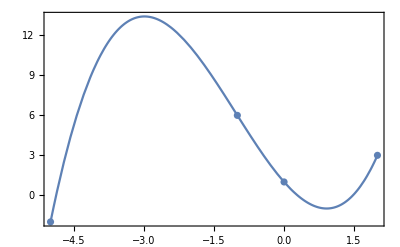

```mathematica
Show[Plot[Subscript[a, 0]+Subscript[a, 1] (x-Subscript[b, 0])+Subscript[a, 2] (x-Subscript[b, 0]) (x-Subscript[b, 1])+Subscript[a, 3] (x-Subscript[b, 0]) (x-Subscript[b, 1]) (x-Subscript[b, 2])/.{Subscript[b, 0]->xxx[[1]],Subscript[b, 1]->xxx[[2]],Subscript[b, 2]->xxx[[3]],Subscript[b, 3]->xxx[[4]],Subscript[a, 0]->-2,Subscript[a, 1]->2,Subscript[a, 2]->-7/5,Subscript[a, 3]->17/35},{x,-5,2}],ListPlot[Table[{xxx[[i]],yyy[[i]]},{i,1,4}]],Frame->True]
```

```mathematica
fac[n_]:=n fac[n-1]
fac[4]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of fac[-1018-1].

Hold[4 fac[4-1]]

```mathematica
taylorS[x_,n_]:=Module[{sum=0},
For[i=0,i<n,i++,delta=x^i/(i!);sum=sum+delta;(*Print[sum]*)];Print[sum]]
```

```mathematica
taylorS[x,10]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880

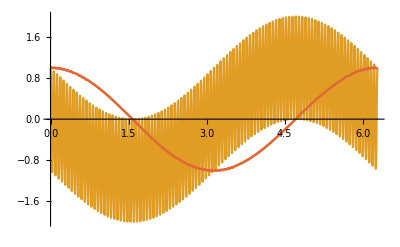

```mathematica
Plot[{-Sin[x],-Sin[x]+0.01 100 Cos[100 x],Cos[x],Cos[x]+0.01 Sin[100 x]},{x,0,2 Pi}]
```

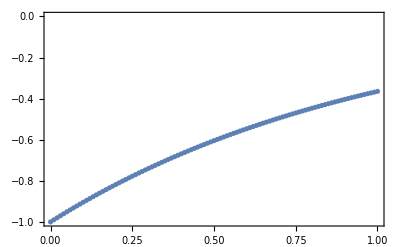

```mathematica
s0=-1;
n=101;
h=0.01;
sss={s0};
tt=Table[t,{t,0,1,h}];
For[i=1,i<n,i++,sf=sss[[i]]+h Exp[-tt[[i]]];AppendTo[sss,sf];(*Print[sss[[i]]];Print[Table[{tt[[i]],sss[[i]]},{i,1,n}]];*)]
Show[ListPlot[Table[{tt[[i]],sss[[i]]},{i,1,n}]],Plot[-Exp[-t],{t,0,1}],Frame->True]
```

```mathematica
Nest[f[x],x f[x-1],x]
```

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[f[x],x f[-1+x],x].

```mathematica
Nest[,x f[-1+x],x]
```

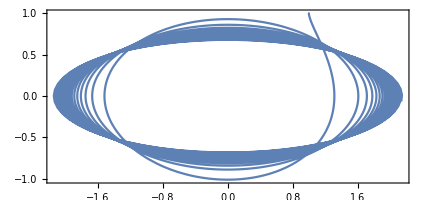

```mathematica
Clear["Global`*"];
sol=DSolve[{x'[t]==t^2 z[t],z'[t]==-t x[t],x[0]==1,z[0]==1},{x,z},t];
ParametricPlot[Evaluate[{x[t],z[t]}/.sol],{t,0,10},Frame->True]
```

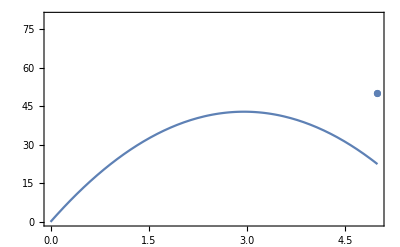

```mathematica
Clear["Global`*"];
sol=DSolve[{x''[t]==-9.8,x'[0]==29,x[0]==0},x,t];
Show[Plot[Evaluate[x[t]/.sol],{t,0,5}],ListPlot[{{5,50}}],Frame->True,PlotRange->{{0,5},{0,80}}]
```

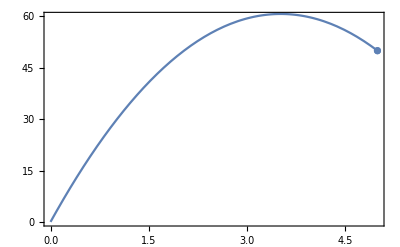

```mathematica
Clear["Global`*"];
sol=DSolve[{x''[t]==-9.8,x'[0]==a,x[0]==0},x,t];
a=Solve[(x[t]/.sol/.t->5)[[1]]==50,a][[2,1,2]]//N[#,10]&;
Show[Plot[Evaluate[x[t]/.sol],{t,0,5}],ListPlot[{{5,50}}],Frame->True,PlotRange->{{0,5},{0,60}}]
```

```mathematica
Clear["Global`*"];
n=10;h=(5-0)/n;a=;
a
```

```mathematica
um=10^-6;
nd=2 10^18;na=8.5 10^16;ni=1.5 10^10;
vb=kB T/e Log[nd na/ni^2]
xn=Sqrt[2 epsilonsi vb/e (na/nd) (1/(na+nd))] 10000
xp=Sqrt[2 epsilonsi vb/e (nd/na) (1/(na+nd))] 10000
w=Sqrt[2 epsilonsi vb/e (na+nd)/(na nd)] 10000
```

0.885655

0.0485231

1.14172

1.19024

```mathematica
Clear["Global`*"];
h=0.5;g=-9.8;
aa={{1,0,0,0,0,0,0,0,0,0,0},{1,-2,1,0,0,0,0,0,0,0,0},{0,1,-2,1,0,0,0,0,0,0,0},{0,0,1,-2,1,0,0,0,0,0,0},{0,0,0,1,-2,1,0,0,0,0,0},{0,0,0,0,1,-2,1,0,0,0,0},{0,0,0,0,0,1,-2,1,0,0,0},{0,0,0,0,0,0,1,-2,1,0,0},{0,0,0,0,0,0,0,1,-2,1,0},{0,0,0,0,0,0,0,0,1,-2,1},{0,0,0,0,0,0,0,0,0,0,1}};
xx={0,g h h,g h h,g h h,g h h,g h h,g h h,g h h,g h h,g h h,50};
yy=Inverse[aa].xx;
tt=Range[0,5,.5];
sol=DSolve[{x''[t]==-9.8,x'[0]==a,x[0]==0},x,t];
a=Solve[(x[t]/.sol/.t->5)[[1]]==50,a][[2,1,2]]//N[#,10]&;
Show[{Plot[Evaluate[x[t]/.sol],{t,0,5},PlotStyle->Gray],ListPlot[Transpose[{tt,yy}],PlotStyle->{Blue}],ListPlot[{{5,50}},PlotStyle->{Dot,Red}]},Frame->True,PlotRange->{{0,5},{0,60}}]
```

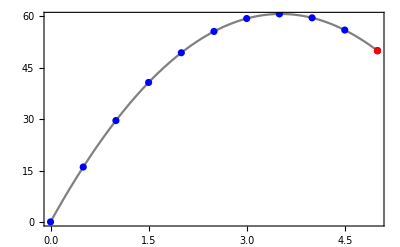

```mathematica
yn1=g h h+2 yy[[1]]-yy[[2]];
v0=(yy[[2]]-yn1)/(2 h)
```

34.5

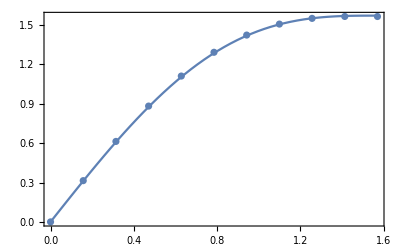

```mathematica
Clear["Global`*"];
n=10;h=Pi/2/n;
aa={{1,0,0,0,0,0,0,0,0,0,0},{1,-2+4 h h,1,0,0,0,0,0,0,0,0},{0,1,-2+4 h h,1,0,0,0,0,0,0,0},{0,0,1,-2+4 h h,1,0,0,0,0,0,0},{0,0,0,1,-2+4 h h,1,0,0,0,0,0},{0,0,0,0,1,-2+4 h h,1,0,0,0,0},{0,0,0,0,0,1,-2+4 h h,1,0,0,0},{0,0,0,0,0,0,1,-2+4 h h,1,0,0},{0,0,0,0,0,0,0,1,-2+4 h h,1,0},{0,0,0,0,0,0,0,0,1,-2+4 h h,1},{0,0,0,0,0,0,0,0,0,2,-2+4 h h}};
xx=Table[ i,{i,0,Pi/2,h}];
yy=Inverse[aa].(4 h h xx)//N;
sol=DSolve[{y''[x]==-4 y[x]+4 x,y[0]==0,y'[Pi/2]==0},y,x];
Show[ListPlot[Transpose[{xx,yy}]],Plot[1/2 (2 x+Sin[2 x]),{x,0,Pi/2}],Frame->True]
```